```mathematica
<<madtomma`madinput`madinput`
```

SetDelayed::write: Tag FindPeaks in FindPeaks[data1_,data2_,Opts___] is Protected.

```mathematica
<<madtomma`madinput`readinmadfiles2`
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jkj62\Documents\GitHub\CBETA

```mathematica
??RunMAD
```

RunMAD[Filename]
RunMAD is used to run the MAD program on a selected input file

RunMAD[Madtomma`MADInput`MADInput`Private`file_]:=Block[{},If[DirectoryName[Madtomma`MADInput`MADInput`Private`file]===,Import[!<>c:\MAD8dl\mad8dl.bat <>Madtomma`MADInput`MADInput`Private`getShortDirectory[]<>\<>ToString[Madtomma`MADInput`MADInput`Private`file],String];,Import[!<>c:\MAD8dl\mad8dl.bat <>ToString[Madtomma`MADInput`MADInput`Private`file],String]];Return[]]

```mathematica
ReadInMADFile["MERGER.MFF"]
```

matrix

matrix

matrix

«1 more identical outputs»

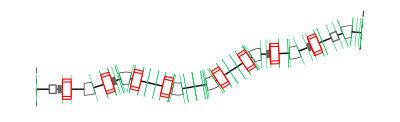

```mathematica
LAT//MADDraw
```

betax, alphax, betay, alphay, dx, dpx

```mathematica
beta0={10.4329,13.1447,13.1042,1.847,0.04066945,0.52648514}
```

{10.4329,13.1447,13.1042,1.847,0.0406695,0.526485}

```mathematica
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
```

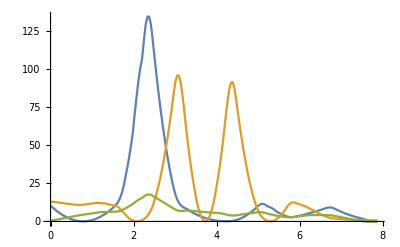

```mathematica
ListLinePlot[{Transpose[{S,BETX}],Transpose[{S,BETY}],Transpose[{S,10 DX}]},PlotRange->All]
```

```mathematica
getTwiss[]:={BETX,ALFX,BETY,ALFY,DX,DPX}[[All,-1]]
```

```mathematica
Unprotect[baseTwiss]
```

{baseTwiss}

```mathematica
baseTwiss=getTwiss[]
Protect[baseTwiss];
```

{0.0795041,0.145028,0.764578,-0.125511,-0.0299682,-0.0593739}

```mathematica
quads=Union[Select[MADFlatten[LAT],#[[2]]==="Quadrupole"&&#[[3]]>0.1&]][[2;;-2]]
```

{{S1$PIP03$MS1020,Quadrupole,0.2,-10.8659,---,---,},{S1$PIP04$MS1022,Quadrupole,0.2,11.0137,---,---,},{S1$PIP05$MS1023,Quadrupole,0.2,-12.6049,---,---,},{S1$PIP08$MS1024,Quadrupole,0.2,-13.0748,---,---,},{S1$PIP09$MS1025,Quadrupole,0.2,10.9554,---,---,},{S1$PIP10$MS1028,Quadrupole,0.193,-13.0516,---,---,}}

```mathematica
startK=#[[4]]&/@quads
```

{-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516}

```mathematica
gradient[data_]:=Block[{k},
k=data[[All,1]];
Coefficient[Fit[Transpose[{k,#}],{1,fitvar},fitvar],fitvar]&/@Rest[Transpose[data]]
]
```

## Try 1

```mathematica
matFunc[quad_,k_]:=Block[{startK},
startK=ToExpression[quad[[1]]][[1,4]];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[k]]];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[startK]]];
Join[{k},baseTwiss-getTwiss[]]
]
```

```mathematica
getMatrixData[]:=Block[{quad=#[[1]],startK=#[[2]]},
testdata=matFunc[quad,#+startK]&/@Range[-0.1,0.1,0.1];
gradient[testdata]/baseTwiss]&/@Transpose[{quads,startK}]
```

```mathematica
startK
```

{-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516}

```mathematica
rmdata=getMatrixData[]
```

{{1.23367,21.3902,-1.31583,6.70264,5.13327,1.85512},{10.9023,174.368,-0.647939,4.97556,36.5104,16.7366},{1.24705,18.5452,-13.3682,88.4344,5.01233,2.85988},{-0.060217,0.223095,-12.5127,86.2339,-0.375932,1.76759},{-0.668588,13.9353,-0.5426,3.16707,-3.71349,7.05992},{-0.0378094,3.88037,-1.41162,12.1334,-0.864149,0.975925}}

```mathematica
testKnobs[knobValues_]:=Block[{},
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,knobValues}];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,startK}];
baseTwiss-getTwiss[]
]
```

```mathematica
Clear[singularValuesDecompositionInverse];
singularValuesDecompositionInverse[list_,n_:All,αin_:0]:=Block[{α=If[αin===0||αin===0.,10^-12,αin]},
{u,w,v}=SingularValueDecomposition[list,n];
(*winv= SparseArray[{i_, i_}:>1/w[[i,i]],Length[w]];*)
winv=SparseArray[{i_, i_}:>w[[i,i]]^1/(w[[i,i]]^2+α^2),Length[w]];
v.winv.ConjugateTranspose[u]
(*PseudoInverse[list,Tolerance->n]*)
]
```

```mathematica
knob[str_,array_]:=startK+str (Transpose[singularValuesDecompositionInverse[rmdata,5,1]].(array/baseTwiss))
```

```mathematica
#/Max[#]&[knob[1,{1,0,0,0,0,0}]-startK]
```

{-2.11682,0.390014,-0.722221,1.,-0.445184,-0.705008}

```mathematica
knob[1,{1,0,0,0,0,0}]-startK
```

{-1.89369,0.348903,-0.646093,0.894591,-0.398257,-0.630694}

```mathematica
startK
```

{-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516}

```mathematica
knob[1,(Transpose[rmdata].startK)]-startK
```

{-1186.74,315.61,-1612.96,1340.7,-553.15,4453.15}

```mathematica
quads[[All,1]]
```

{S1$PIP03$MS1020,S1$PIP04$MS1022,S1$PIP05$MS1023,S1$PIP08$MS1024,S1$PIP09$MS1025,S1$PIP10$MS1028}

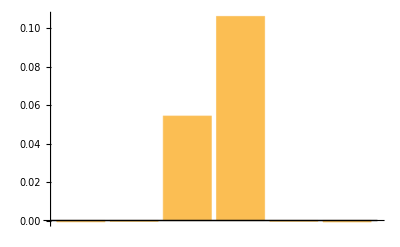

```mathematica
testKnobs[knob[0.1,{0,0,0,1,0,0}]]//BarChart
```

## Try 2

```mathematica
matFunc[quad_,k_]:=Block[{startK},
startK=ToExpression[quad[[1]]][[1,4]];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[k]]];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[startK]]];
Join[{k},baseTwiss-getTwiss[]]
]
```

```mathematica
getMatrixData[]:=Block[{quad=#[[1]],startK=#[[2]]},
testdata=matFunc[quad,#+startK]&/@{0.001,0.001,0.001};
gradient[testdata]/(0.001 baseTwiss)]&/@Transpose[{quads,startK}]
```

```mathematica
testdata
```

{{6.65918,0.,0.,0.,0.,0.,0.},{6.65918,0.,0.,0.,0.,0.,0.},{6.65918,0.,0.,0.,0.,0.,0.}}

```mathematica
startK
```

{1.56954,-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516,-13.0516,6.65818,6.65818}

```mathematica
rmdata=getMatrixData[]
```

{{-0.161464,-3.81237,-0.349215,3.0994,0.616949,-0.351124},{-0.0309847,-0.441253,0.0428385,-0.236498,-0.334506,-0.0967067},{0.436912,7.47975,-0.0118696,0.155038,1.7512,0.770699},{-0.0273587,-0.266039,0.524771,-3.4075,-0.283598,-0.123175},{0.0233431,0.452638,0.472359,-3.20507,-0.0677463,-0.0770188},{-0.055881,0.0926727,-0.00715968,0.0731973,-0.0711138,0.333341},{0.0212149,0.455849,-0.013374,0.0470822,-0.0808787,-0.011225},{0.0225167,0.311742,0.0394207,-0.405091,-0.0492416,-0.0468354},{-0.0398759,-0.873457,0.0276827,-0.111445,0.155005,0.0182058},{0.,0.,0.,0.,0.,0.}}

```mathematica
testKnobs[knobValues_]:=Block[{},
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,knobValues}];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,startK}];
baseTwiss-getTwiss[]
]
```

```mathematica
Clear[singularValuesDecompositionInverse];
singularValuesDecompositionInverse[list_,n_:All,αin_:0]:=Block[{α=If[αin===0||αin===0.,10^-12,αin]},
{u,w,v}=SingularValueDecomposition[list,n];
(*winv= SparseArray[{i_, i_}:>1/w[[i,i]],Length[w]];*)
winv=SparseArray[{i_, i_}:>w[[i,i]]^1/(w[[i,i]]^2+α^2),Length[w]];
v.winv.ConjugateTranspose[u]
(*PseudoInverse[list,Tolerance->n]*)
]
```

```mathematica
knob[str_,array_]:=startK+str (Transpose[singularValuesDecompositionInverse[rmdata,4,1]].(baseTwiss*array))
```

```mathematica
#/Max[#]&[knob[1,{1,0,0,0,0,0}]-startK]
```

{1.,0.220083,0.871988,0.184031,0.629893,-3.37867,0.472207,0.663067,-0.873919,0.}

```mathematica
knob[1,{1,0,0,0,0,0}]-startK
```

{0.00109701,0.000241433,0.000956579,0.000201883,0.000690998,-0.00370643,0.000518015,0.00072739,-0.000958697,0.}

```mathematica
startK
```

{1.56954,-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516,-13.0516,6.65818,6.65818}

```mathematica
knob[1,(Transpose[rmdata].startK)]-startK
```

{-1.76129,0.270357,0.227964,0.724313,0.728739,-0.413151,0.241159,0.273629,-0.454478,0.}

```mathematica
quads[[All,1]]
```

{S1$PIP02$MS1019,S1$PIP03$MS1020,S1$PIP04$MS1022,S1$PIP05$MS1023,S1$PIP08$MS1024,S1$PIP09$MS1025,S1$PIP10$MS1027,S1$PIP10$MS1028,S1$PIP11$MS1030,S1$PIP11$MS1031}

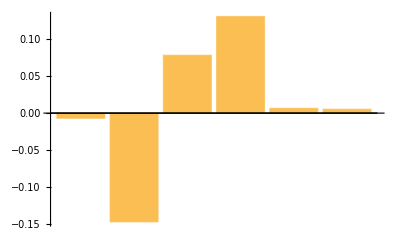

```mathematica
testKnobs[knob[1,{0,0,0,0,0,1}]]//BarChart
```

## Optimiser

```mathematica
testKnob[knobValues_, n_:1]:=Block[{},
Close[#]&/@Drop[Streams[],2];
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,knobValues}];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,startK}];
(1+(100((0.1-#[[n]])^2&[baseTwiss-getTwiss[]])))/Min[Abs[(#[[n]])/Drop[#,{n}]&[baseTwiss-getTwiss[]]]]^2
]
```

```mathematica
testKnob[knob[1,{0,1,0,0,0,0}],2]
```

1.11688

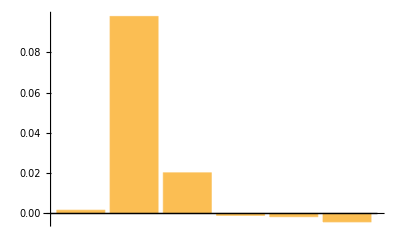

```mathematica
testKnobs[knob[0.1,{0,1,0,0,0,0}]]//BarChart
```

```mathematica
optFunc[quadvalues_,n_:1]:=Block[{},
Total[testKnob[startK+#(quadvalues-startK),n]&/@{0.01,0.1,1}]
]
```

```mathematica
knob[1,{0,1,0,0,0,0}]
```

{-10.8511,11.0569,-12.7569,-13.0025,10.912,-12.4696}

```mathematica
optFunc[knob[0.1,{0,1,0,0,0,0}],2]
```

0.224323

```mathematica
<<optimise`simplexoptimise`
```

```mathematica
ReplacePart[Table[0,6],3->1]
```

{0,0,1,0,0,0}

```mathematica
knobALFX={-10.81477556155196,11.0118880268269,-12.620930049933927,-13.066298822849568,10.952915412342954,-13.021865004596268};
```

```mathematica
knobBETY={};
```

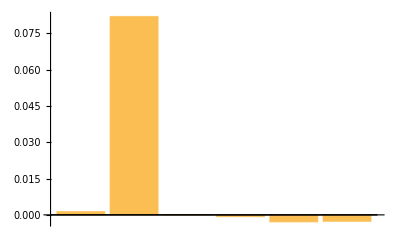

```mathematica
testKnobs[startK+1(knobALFX-startK)]//BarChart
```

```mathematica
n=1;
startsimplex=knob[0.1,ReplacePart[Table[0,6],n->1]]
```

{-11.0553,11.0486,-12.6695,-12.9853,10.9156,-13.1147}

```mathematica
n=3;
simplexans=knob[0.1,ReplacePart[Table[0,6],n->1]];
{simplexfit,simplexans}=SimplexOptimise3[Length[startsimplex],{0.8,1.2}#&/@startsimplex,100,optFunc[#,n]&,StartSimplex->simplexans]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

```mathematica
{simplexfit,simplexans}=SimplexOptimise3[Length[startsimplex],{0.9,1.1}#&/@simplexans,100,(optFunc[#,n]&),StartSimplex->simplexans]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

run out

Minimum Fitness: 0.1648	Raw Value: {1.42078,-10.2906,10.9262,-12.5689,-13.1417,11.1325,-12.0605,-13.3209,5.53821,6.80474}	Total No. Iterations: 244	Number Restarts = 1

{0.1648,{1.42078,-10.2906,10.9262,-12.5689,-13.1417,11.1325,-12.0605,-13.3209,5.53821,6.80474}}

```mathematica
n=5;
simplexans=knob[0.1,ReplacePart[Table[0,6],n->1]];
{simplexfit,simplexans}=SimplexOptimise3[10,{0.8,1.2}#&/@startsimplex,100,optFunc[#,n]&,StartSimplex->simplexans]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

run out

Minimum Fitness: 2.26929	Raw Value: {1.89812,-10.931,10.9888,-12.672,-13.0705,11.0669,-12.332,-12.9405,6.70612,7.13428}	Total No. Iterations: 247	Number Restarts = 1

{2.26929,{1.89812,-10.931,10.9888,-12.672,-13.0705,11.0669,-12.332,-12.9405,6.70612,7.13428}}

```mathematica
{simplexfit,simplexans}=SimplexOptimise3[10,{0.9,1.1}#&/@simplexans,100,(optFunc[#,n]&),StartSimplex->simplexans]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

Minimum Fitness: 2.15035	Raw Value: {1.8933,-10.922,10.9886,-12.6693,-13.0715,11.0379,-12.4648,-12.9374,6.71051,7.15014}	Total No. Iterations: 98	Number Restarts = 1

{2.15035,{1.8933,-10.922,10.9886,-12.6693,-13.0715,11.0379,-12.4648,-12.9374,6.71051,7.15014}}

```mathematica
n=6;
startsimplex=knob[0.1,ReplacePart[Table[0,6],n->1]];
{simplexfit,simplexans}=SimplexOptimise3[10,{0.8,1.2}#&/@startsimplex,100,optFunc[#,n]&,StartSimplex->startsimplex]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

Minimum Fitness: 0.488125	Raw Value: {1.93536,-10.9295,11.0524,-12.6221,-13.1089,10.272,-13.0792,-12.8332,7.48131,6.99386}	Total No. Iterations: 250	Number Restarts = 1

{0.488125,{1.93536,-10.9295,11.0524,-12.6221,-13.1089,10.272,-13.0792,-12.8332,7.48131,6.99386}}

```mathematica
{simplexfit,simplexans}=SimplexOptimise3[10,{0.9,1.1}#&/@simplexans,100,(optFunc[#,n]&),StartSimplex->simplexans,CompressionFactor->1.2,ExpansionFactor->1.2]
```

Last Worst Value = 	Expansion/Compression = /	Converge =

run out

Minimum Fitness: 0.370618	Raw Value: {1.84887,-10.8716,11.042,-12.6036,-13.1192,10.2928,-12.6915,-12.8739,7.25007,6.99438}	Total No. Iterations: 176	Number Restarts = 1

{0.370618,{1.84887,-10.8716,11.042,-12.6036,-13.1192,10.2928,-12.6915,-12.8739,7.25007,6.99438}}

```mathematica
SimplexFinish[]
```

False

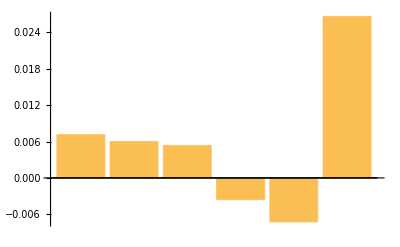

```mathematica
testKnobs[startK+0.1(simplexans-startK)]//BarChart
```